# Vaje za 2. teden

26. 2. 2026

## Ponovitev

Izračunaj 1+x+x^2+x^3, kjer je x = 1/√e+1/√π, na dva načina: naprej s pomočjo prepisovalnega pravila, nato pa še tako, da definiraš vrednost spremenljivke x.
Spremenljivko x na koncu pobriši.

```mathematica
N[1 + x + x^2/. x -> 1/√e+1/√π]
```

2.93478+1/(√e)

```mathematica
x = 1/√Exp[1]+1/√Pi;
(*f[x_]:=1 + x + x^2*)
N[1 + x + x^2]
```

```mathematica
3.5413061312400558
Clear[x]
```

3.54131

## Naloga 1

Izračunaj 1000-i decimalki števil e in π na dva načina:
1. Tako da izračunaš dovolj decimalk obeh števil in pogledaš ustrezno decimalko pri koncu. Uporabi funkcijo N tako, da ji podaš natančnost.
2. Z uporabo funkcije RealDigits in izpisom ustreznega elementa seznama.

Določi še 5., 100. in 443. decimalko.

Napiši fuknkcijo, ki sprejme poljubno realno število x in naravno število n in vrne n-to decimalko števila x.

```mathematica
(*1*)
```

```mathematica
Mod[N[Pi,1001]*10^1000,10]
```

9.

```mathematica
ResourceFunction["NthDigit"][Pi, 1001]
```

9

```mathematica
ResourceFunction["NthDigit"][E, 1001]
```

4

```mathematica
Mod[N[E,1001]*10^1000,10]
```

4.

## Naloga 2

V Matematico vnesi izraz sin(π/8)+cos(π/8). Kaj Mathematica vrne? Nato poskusi ta izraz poenostaviti s primernim izrazom (končni rezultat se “lepo” izrazi s koreni).Definiraj niz niz, ki bo lepo predstavil in zapisal rešitev te naloge. Po klicu spremenljivke niz naj tako Mathematica izpiše spodnji niz, kjer naj bo niz “___” nadomeščen s pravim rezultatom.
"Vsota sin(π/8) + cos(π/8) je enaka ___."

```mathematica
Sin[Pi/8]+Cos[Pi/8]
```

Cos[π/8]+Sin[π/8]

```mathematica
Sin[Pi/8]+Cos[Pi/8]//FullSimplify
```

√(1+1/(√2))

```mathematica
niz1 = TemplateApply["Vsota sin(π/8) + cos(π/8) je enaka <*FullSimplify[Sin[Pi/8]+Cos[Pi/8]]*>."];
niz2 = StringForm["Vsota sin(π/8) + cos(π/8) je enaka ``.", Sin[Pi/8]+Cos[Pi/8]//FullSimplify];
```

```mathematica
niz1
niz2
```

Vsota sin(π/8) + cos(π/8) je enaka 1.30656.

Vsota sin(π/8) + cos(π/8) je enaka √(1+1/(√2)).

## Naloga 3

Napiši  funkcijo poenostaviInIzpisi, ki  bo  sprejela  izraz “izr”, ga  poenostavila  in  rezultat  izpisala  v  obliki
“Izraz [izr] se poenostavi v izraz [poenostavljen_izraz]”,
kjer je [izr] nadomestite z vnešenim izrazom, [poenostavljen_izraz] pa s poenostavljenim izrazom.

```mathematica
poenostaviInIzpisi[izr_]:= StringForm["Izraz `` se poenostavi v izraz ``",izr,izr//FullSimplify]
```

```mathematica
poenostaviInIzpisi[Sin[Pi/8]+Cos[Pi/8]]
```

Izraz Cos[π/8]+Sin[π/8] se poenostavi v izraz √(1+1/(√2))

## Naloga 4

Matej ima 249 jabolk, Jana pa 419 jabolk. Koliko jabolk imata skupaj?
Rešitev zgornje naloge predstavi z nizom, ki ga shrani v spremenljivki niz. Ob klicu spremenljivke niz naj Mathematica vrne:
“Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.”
Pomagaj si z vodičem za generiranje nizov (predvsem del za vstavljanje izrazov) in uporabi funkcijo TemplateApply, da definiraš zgornji niz še brez direktnega vnašanja števila 668.

```mathematica
niz = TemplateApply["Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = <*249+419*> jabolk."]
```

Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.

## Naloga 5

1. Definiraj funkcijo f(x)=x^2+3x+2+sin(x).
2. Izračunaj f(3)+f(4).  Uporabi tako prefiksni kot postfiksni način klica funkcije. Rezultat izpiši numerično (kot približek).
3. Nariši graf funkcije f na intervalu [-10,10].
4. Definiraj funkcijo g z istim predpisom kot f, pri čemer g definiraj kot anonimno funkcijo s formalnim parametrom #.
5. Definiraj funkcijo h(x,y)=(f(x)+g(y))^2 na dva načina: na standardni način in kot anonimno funkcijo.

```mathematica
(*1*)
```

```mathematica
f[x_]:=x^2+3x+2+Sin[x]
```

```mathematica
(*2*)
```

```mathematica
f[3]+f[4]//N
```

49.3843

```mathematica
(3//f) + (4//f)//N
```

49.3843

```mathematica
(*3*)
```

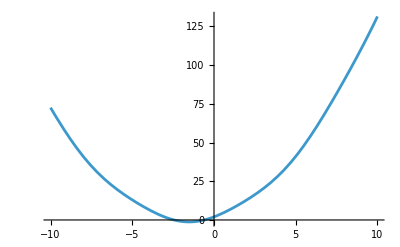

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
(*4*)
```

```mathematica
g = #^2+3#+2+Sin[#]&;
```

```mathematica
(*5*)
```

```mathematica
h[x_]:=(f[x]+g[y])^2
```

```mathematica
h = (f[#]+g[#])^2;
```

## Naloga 6

1. Definiraj funkciji f(x) in g(n), kjer je f(x)=x^3+x+1, g(n) pa je ostanek števila n pri deljenju s 7.
2. Ustvari seznam {f(1),f(2),...,f(100)}. Poišči vsa števila n s tega seznama, za katere je g(n)=3. Uporabi ukaz Select.
3. Poskusi rešiti zgornjo nalogo v eni vrstici s pomočjo uporabe anonimnih funkcij.

```mathematica
(*1*)
```

```mathematica
Clear[f,g];
```

```mathematica
f[x_] := x^3+x+1
g[n_]:= Mod[n,7]
```

4

```mathematica
(*2*)
```

```mathematica
seznamF = f/@ Range[100];
Select[seznamF, g[#] == 3&]
```

{3,31,521,1011,3391,4931,10671,13849,24419,29823,46693,54911,79551,91171,125051,140661,185251,205439,262209,287563,357983,389091,474631,512081,614211,658591,778781,830679,970399}

```mathematica
(*3*)
```

```mathematica
Select[f/@ Range[100],  g[#] == 3&]
```

{3,31,521,1011,3391,4931,10671,13849,24419,29823,46693,54911,79551,91171,125051,140661,185251,205439,262209,287563,357983,389091,474631,512081,614211,658591,778781,830679,970399}

## Naloga 7

Kaj vrne spodnja koda? Pojasni vsako vrstico!

```mathematica
VsotaKvadratov[x_,y_]:=x^2+y^2 (*ne vrne ničesar, le definira funkcijo VsotaKvadratov, ki sprejme dva argumenta in vrne... vsoto njunih kvadratov*)
AplicirajFunkcijo2Spremenljivk[f_,x_,y_]:=f[x,y] (* pravtako ne vrne ničesar, ko pa jo uporabimo vrne vrednost funkcije f z argumentoma x in y*)
AplicirajFunkcijo2Spremenljivk[VsotaKvadratov,3,4] (*vrne 25*)
```

Zgornja koda vsebuje 3 vrstice. Zapiši ekvivalent te kode z uporabo anonimne funkcije, ki vsebuje le 1 vrstico.

```mathematica
(#1^2+#2^2&)[3,4]
```

25

## Naloga 8

Nariši graf funkcije f (x, y, z) = x  sin (xy)  cos (xy + z), kjer za z-koordinato uporabi  slider.

```mathematica
f[x_,y_,z_]:=x Sin[x y] Cos[x y + z]
```

```mathematica
Manipulate[Plot3D[f[x,y,z],{x,-10,10},{y,-10,10}],{z,-1,1}]
```